## Wolfram Biology 101

## Who is Stephen?

## Background: The First Taste of Self-Discovery

```mathematica
-Graphics--Graphics-
```

## Plot-twist: Mathematica and Computation

## A Minimal Model for Complexity

## The Breakthrough: rule 30

```mathematica
-Graphics--Graphics-
```

## Simple Programs in Biology: Pigmentation

### The Case of Shells

-Graphics-

## Simple Programs in Biology: Pigmentation

### The Case of Shells: 1D Cellular Automata Model

-Graphics-

## Simple Programs in Biology: Pigmentation

### Other Species

## Simple Programs in Biology: Pigmentation

### 2D Cellular Automata Model

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{1,1,-0.4,-0.4},{1,1,-0.2,-0.2}}}],ImageSize->700]
```

-Graphics-

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{{1,1},{1,1},{-0.4,0},{-0.4,0}},{{1,1},{1,1},{0,-0.6},{0,-0.6}}}}],ImageSize->700]
```

-Graphics-

## But How Powerful is Evolution?

```mathematica
CloudGet["https://wolfr.am/nks-page0345a-graphic"]
```

-Graphics-

## Growth and Shape: The Case of Leaves

```mathematica
CloudGet["https://wolfr.am/nks-page0403a-graphic"]
```

-Graphics-

## Growth and Shape: The Case of Leaves

```mathematica
GraphicsColumn[GraphicsRow[Flatten@{Graphics[{Line[#[[1]]],With[{head=#[[1,1,2]]},{Disk[head,.1],Arrowheads[.125,1.5],Arrow[{{head[[2]]-.4,head[[2]]},{head[[2]]+.4,head[[2]]}}]}],Translate[{Line[Flatten[#[[1;;2]],1]],Disk[#,.1]&/@#[[2,All,2]]},{2.5,0}]},Sequence[ImageSize->{Automatic,40},Frame->True,FrameTicks->False,FrameStyle->AbsoluteThickness[1],PlotRange->{{-0.75,3.4},{-0.25,2.25}}]]&@#[[4]],Graphics[{AbsoluteThickness[.3],Line/@#},Sequence[Frame->True,FrameTicks->False,PlotRange->All,PlotRangePadding->Scaled[0.05],FrameStyle->AbsoluteThickness[1]]]&/@#}&@With[{grow=#},Table[NestWhileList[Flatten[With[{head=#[[2]],dir=#[[2]]-#[[1]]},{head,head+#}&/@ReIm@grow[dir[[1]]+dir[[2]] I]]&/@#,1]&,{{{0,0},{0,1}}},(Length[#]<500&)],{θ,120 °,15 °,-15 °}]],ImageSize->{750,Automatic}]&/@Table[Function[Evaluate@Table[With[{t=θ ((2 i-2)/(Length[lengths]-1)-1)},# lengths[[i]] (Cos[t]+Sin[t] I)],{i,Length[lengths]}]],{lengths,{{.4,.7,.4},{.5,.4,.5},{.5,.5,.5},{.5,.6,.5},{.55,.8,.55},{.7,.8,.7},{.65,.6,.65},{.5,.6,.6,.5},{.65,.65}}}],ImageSize->Large]
```

-Graphics-

## Conclusion

Computational irreducibility is a stronger force than evolution

## The Recent Breakthrough: A Minimal Model for Biological Evolution

```mathematica
deathdiff[rule_,t_:100,max_:150]:=With[{array=CellularAutomaton[rule,{{1},0},{max,All}]},Abs[LengthWhile[Reverse[array],Total[#]==0&]-(max-t)]]
```

```mathematica
randrulesx[rule_,n_Integer,k_:5]:=FromDigits[#,k]&/@With[{dig=IntegerDigits[rule,k,k^3]},Union[Table[ReplacePart[dig,RandomInteger[{1,Length[dig]-1}]->RandomInteger[{0,k-1}]],n]]]
```

```mathematica
Grid[Partition[Framed[ArrayPlot[CellularAutomaton[#,{{1},0},{55,{-14,14}}],GridLines->{None,{5}},
GridLinesStyle->Directive[Thickness[.015],GrayLevel[0,.8]],ColorRules->{0->White,1->Hue[0.08, 1, 1],2->Hue[0.75, 0.86, 0.8200000000000001],3->Hue[0.14, 0.81, 0.99]},
Frame->None,ImageSize->50],FrameStyle->GrayLevel[0, 0.3],FrameMargins->0]&/@(SeedRandom[7067];With[{k=3},
NestList[{First[First[SortBy[{#,deathdiff[{#,k,1},50,100]}&/@randrulesx[#[[1]],100,k],Last]]],k,1}&,
{k RandomInteger[k^k^3/k],k,1},20]]),10],Spacings->{.25,.25}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## The New Minimal Model for Biological Evolution: Explained

### Start from the “null” rule

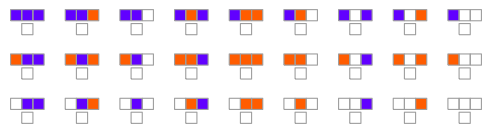

```mathematica
RulePlot[CellularAutomaton[{0, 3, 1}], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

## The New Minimal Model for Biological Evolution: Explained

### Evolution of the genotype

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
keptrus = First/@Split[First/@e3];
```

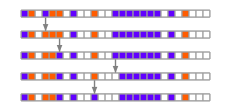
-Graphics-
⋮
-Graphics-
⋮

```mathematica
Column[{{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[keptrus][[1;;5]],(*"Arrows"->"Line",*)ImageSize->300],"⋮",{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[keptrus][[100;;104]],(*"Arrows"->"Line",*)ImageSize->300],"⋮"},Center]
```

## The New Minimal Model for Biological Evolution: Explained

### Evolution of the phenotype

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
evo=Map[DeleteDuplicates,SplitBy[e3,Last]];
```

```mathematica
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7},
Mesh->True,MeshStyle->Opacity[.1] ]]&,
evo,{2}];
```

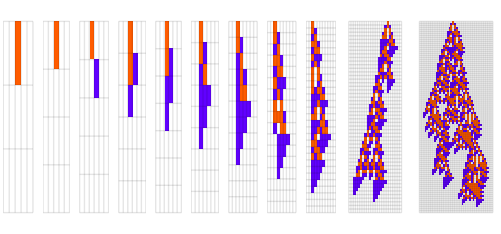

```mathematica
GraphicsRow[First/@res]
```

## Idealized Computational Organisms

```mathematica
es = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+#];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]]&/@ {54, 60, 16};
```

```mathematica
evos=Map[DeleteDuplicates,SplitBy[#,Last]]&/@es;
```

```mathematica
ress=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,10(Length[data]+1)^.7} ]]&,
#,{2}]&/@ evos;
```

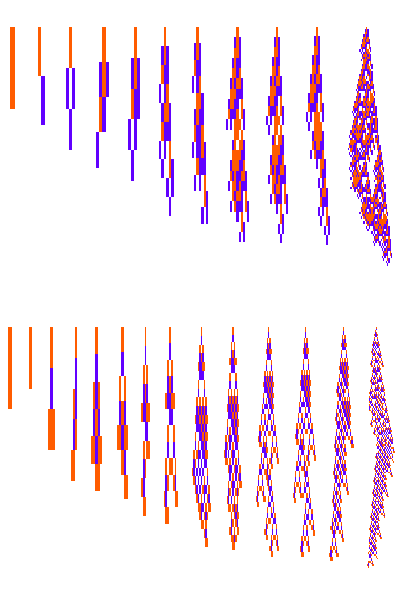

```mathematica
Column[GraphicsRow[First/@#]&/@ Prepend[ress[[;;-2]], ress[[-1]]][[;;2]]]
```

## Computational Irreducibility is a Stronger Force than Natural Selection

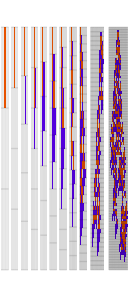

## How Common is Irreducible Behavior in Adaptive Systems?

### Other rule spaces

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
evos = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+#];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
]&/@ {181, 43};
```

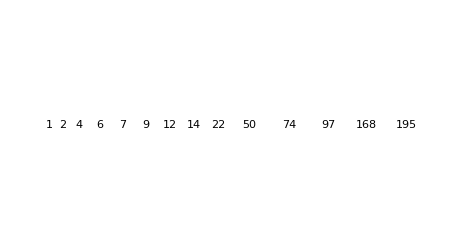

```mathematica
GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,16 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@Rest[#[[ResourceFunction["ProgressiveMaxPositions"][#[[All,-1]]]]]]]&@ evos[[1]]
```

## How Common is Irreducible Behavior in Adaptive Systems?

### Other fitness functions: width

```mathematica
Module[{
k=3,r=1,cut=800,deep=5000,fun=Length@*First,
init,evo,ru,data,lt,test,mask,canonical,res},
res=[[{1, 3}]];
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,Min[20(Length[data]+1)^.7,600]}]]&,
res,{2}];
GraphicsColumn[GraphicsGrid[{#}]&/@res,Automatic,0]
]
```

-Graphics-

## How Common is Irreducible Behavior in Adaptive Systems?

### Other fitness functions: aspect ratio

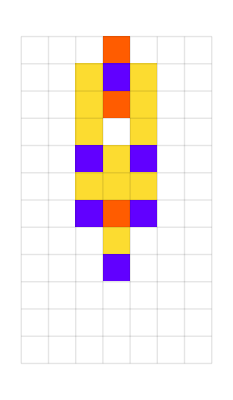
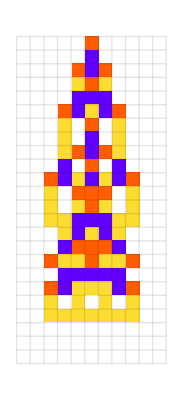
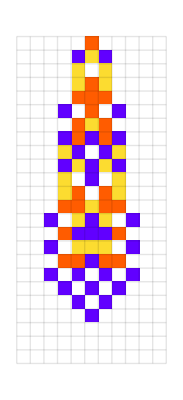
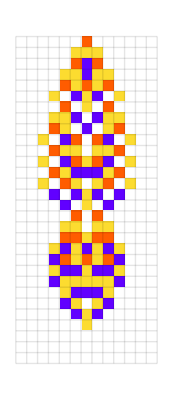
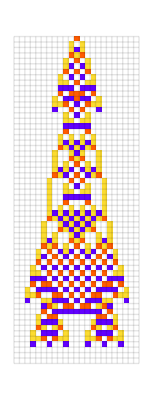
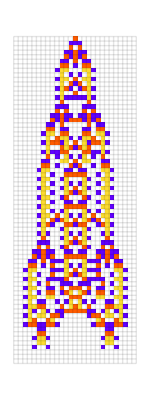
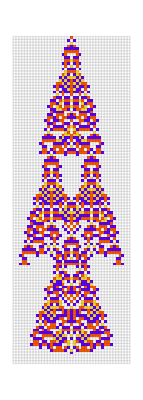
{-Graphics-{9,3},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{27,9},-Graphics-{57,19},-Graphics-{69,23},-Graphics-{111,37}}

```mathematica
Style[With[{data=CellularAutomaton[
#[[1]],{{1},0},#[[2,1]]+2]},
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,20Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
],Style[#[[2]],"Text",Italic,Gray,11]]]&/@{{{109636419052937157723438118980837975564,4,1},{9,3}},{{74948306682547943335519680440646385168,4,1},{21,7}},{{193649253952380488246394671786963518216,4,1},{21,7}},{{246493520306698100424983701858655419148,4,1},{27,9}},{{280384207228392989942672757173339297804,4,1},{57,19}},{{330335253914559274144004959766636949128,4,1},{69,23}},{{142140648448642989785750794400464692296,4,1},{111,37}}}, LineSpacing->{1,1}]
```

## How Common is Irreducible Behavior in Adaptive Systems?

### More dimensions

```mathematica
allrules=;
```

```mathematica
Row[Labeled[ArrayPlot3D[CellularAutomaton[<|"RuleNumber"->#[[1,1]],"Neighborhood"->9,"Dimension"->2,"Colors"->2|>,{CrossMatrix[1],0},#[[1,2]]],Method->{"ShrinkWrap"->True},ImageSize->{Automatic,15(#[[1,2]])^.5},Lighting->,ColorRules->{1->Hue[0.06, 0.93, 0.96]},Mesh->None],Text[Style[#[[1,2]]-1,Small]]]&/@allrules[[190]]]
```

-Graphics3D-0-Graphics3D-1-Graphics3D-3-Graphics3D-4-Graphics3D-6-Graphics3D-12-Graphics3D-14-Graphics3D-49-Graphics3D-93-Graphics3D-145-Graphics3D-147-Graphics3D-163-Graphics3D-166-Graphics3D-235

## New Ideas: What Does the Fitness Landscape Look Like?

-Graphics-

## New Ideas: What Does the Fitness Landscape Look Like?

-Graphics-

## New Ideas: The Computational “Tree of Life”

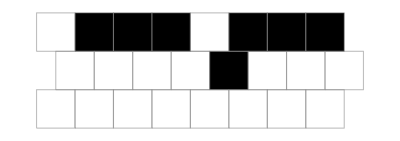
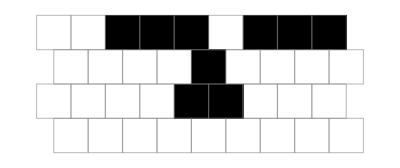
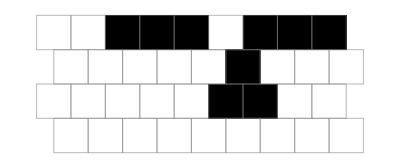
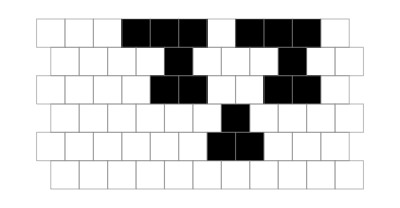
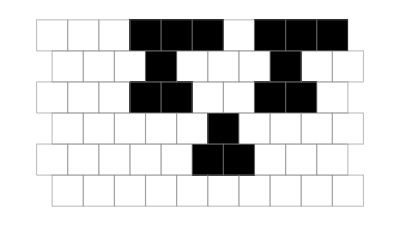
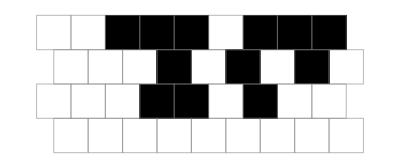
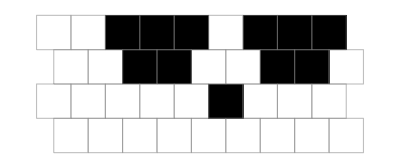
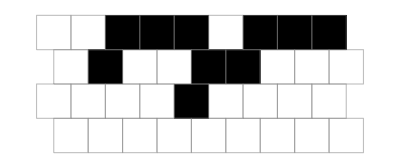

```mathematica
Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{Automatic,(2+key[[1]])10}]
&@First[Union[CellularAutomaton[{#,2,3/2},{{1,1,1,0,1,1,1},0},
key[[1]]]&/@rules]]
],sublevels]];
Graph[res,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
]
```

## New Ideas: The “Evolutionary Observer”

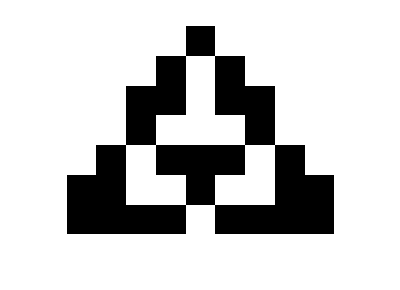
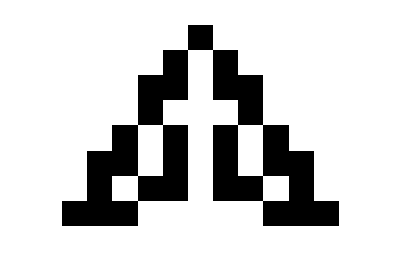
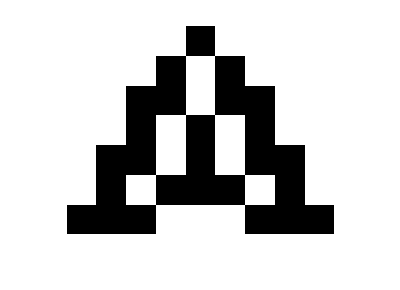
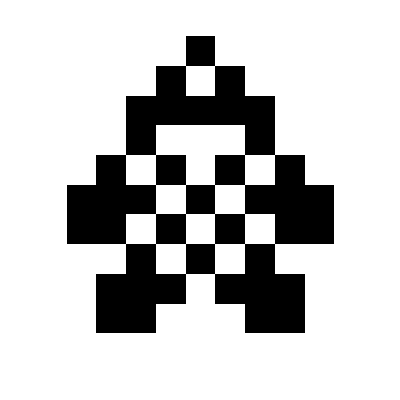
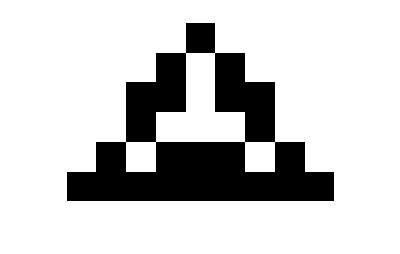
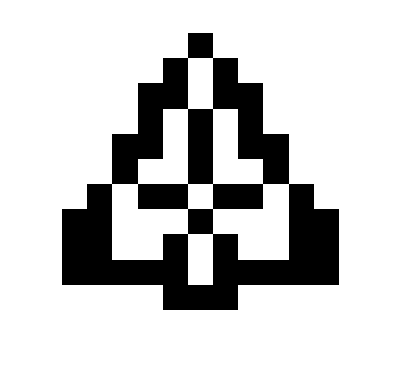
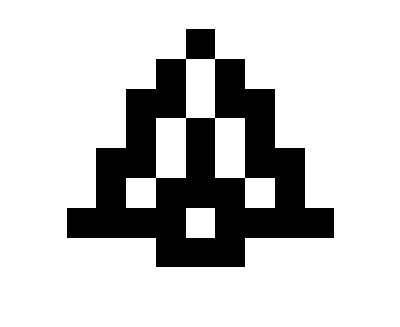
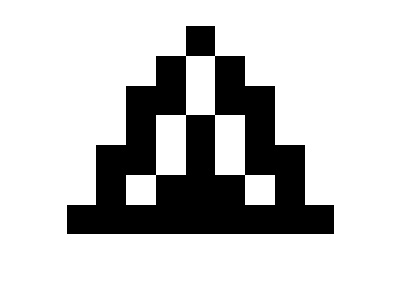

```mathematica
Module[{g1},
g1=VertexOutComponentGraph[{{"[◼]", "EvolutionaryMultiwayGraph"}}[{
{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
{{"[◼]", "changeFitness"}}[{2,2},{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
Length@*First]},
GraphLayout->"LayeredDigraphEmbedding",
"Reduced"->False,
AspectRatio->1,
EdgeStyle->{x_:>Association[
{1}->Directive[Hue[0.45, 0.54, 0.74],Thick,Opacity[8]],{2}->Directive[Hue[0.06, 0.96, 0.98],Thick,Opacity[8]],
{1,2}->Directive[{Hue[0.6,0.3,0.5,.35]}]
][Last[x]]}
],{{0,65815}}];
Legended[{{"[◼]", "addVertexFigures"}}[g1,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],{2,2},
"VertexFigures"->1,VertexSize->1.2,AspectRatio->.7,ImageSize->550],LineLegend[{Directive[Hue[0.45, 0.54, 0.74],Thick,Opacity[8]],Directive[Hue[0.06, 0.96, 0.98],Thick,Opacity[8]],Directive[{Hue[0.6,0.5,0.5,.6]}]},{"height","width","both"}]]]
```

## Beyond Biology: Machine Learning

```mathematica
(*experiment=TrainPiecewise[RRnet[{5,5,5,5}],TargetDevice->"GPU"][[-1,-1]];*)
```

```mathematica
experiment=CloudImport[CloudObject[["https://www.wolframcloud.com/obj/c761ecc0-3ebf-414c-8642-292771f7efa9"](https://www.wolframcloud.com/obj/c761ecc0-3ebf-414c-8642-292771f7efa9)]];
```

```mathematica
labels=
{{"[◼]", "WritingsStyleData"}}["MachineLearning"]["GrayLabelingFunction"]/@{x,f[x]};
```

```mathematica
Plot[{experiment[x],piecewise[x]},{x,-3,3},Frame->True,FrameTicks->None,FrameLabel->labels,RotateLabel->False,PlotStyle->{Automatic,Directive[Gray,Dotted]},Exclusions->None,PlotRange->{{-3,3},{-0.4,1.4}},ImageSize->90]
```

-Graphics-

```mathematica
Options[RuleArray]={"Radius"->1/2,"Orientation"->"Both","Neighborhood"->"Alternating","Function"->"FinalState"};
```

```mathematica
oneZeroOneOneFunction=Piecewise[{{0,#<-2},{1,#<-1},{0,#<0},{1,#<2}}]&;
```

```mathematica
BricksPlotDrawCell["Hexagonal",height_Integer][row_Integer,col_Integer]:=With[{x=N[col+If[Mod[row,2]==0,1/2,0]-1],y=N[height-row]},Rotate[RegularPolygon[N@{Sin[Pi/3] x,3/2 Sin[Pi/6] y},1/2,6],Pi/6.]]
```

```mathematica
(*result=With[{raHeight=30,raWidth=20,rules={8,6},opts=Sequence["Radius"->1/2,"Orientation"->"Both","Neighborhood"->"Alternating","Appearance"->"Hexagonal"]},
With[{raOpts=Sequence@@FilterRules[{opts},Options[RuleArray]]},
With[{fn=(x|->Rescale[oneZeroOneOneFunction[Rescale[x,{1,raWidth},{-3,3}]],{0,1},{Floor[raWidth*1/4],Floor[raWidth*3/4]}])},
With[{seed=30498504},
SeedRandom[seed];
With[{loss={{"[◼]", "FunctionWithZerosLoss"}}[fn]},
With[{lossFn=loss[raHeight,raWidth,raOpts]},
{{"[◼]", "AdaptRuleArray"}}[ConstantArray[1,{raHeight,raWidth}],rules,50000,lossFn,raOpts]
]
]
]
]
]
];*)
```

```mathematica
(*bestResult=Last[result];*)
```

```mathematica
bestResult=CloudImport[CloudObject[["https://www.wolframcloud.com/obj/022bbd93-4d41-4796-88f7-b0b5d5db5f9f"](https://www.wolframcloud.com/obj/022bbd93-4d41-4796-88f7-b0b5d5db5f9f)]];
```

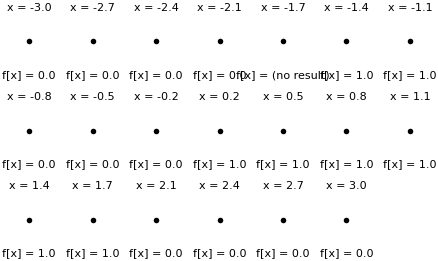

```mathematica
GraphicsGrid[Partition[With[{raHeight=30,raWidth=20,rules={8,6},opts=Sequence["Radius"->1/2,"Orientation"->"Both","Neighborhood"->"Alternating",Appearance->"Hexagonal",Mesh->False]},
With[{raOpts=Sequence@@FilterRules[{opts},Options[RuleArray]]},
With[{fn=(x|->Rescale[
oneZeroOneOneFunction[
Rescale[x,{1,raWidth},{-3,3}]
],{0,1},{Floor[raWidth*1/4],Floor[raWidth*3/4]}]),finalStateFn={{"[◼]", "RuleArrayFinalState"}}[raOpts]},
With[{ruleArray=First[bestResult]},
Table[
With[{init=ReplacePart[Table[0,raWidth],x->1],target=ReplacePart[Table[0,raWidth],fn[x]->1]},
With[{finalState=finalStateFn[init,{{"[◼]", "IndicesToRules"}}[ruleArray,rules],raHeight]},
With[{pos=Position[finalState,1,1,1]},
With[{y=If[Length[pos]==0,Infinity,First[First[pos]]]},
GraphicsColumn[
Append[
Text[#[[3]][NumberForm[N[First[#]],{#[[2]],1}]]]&/@{
{Rescale[x,{1,raWidth},{-3,3}],2,Row[{Style["x = ",Italic,Gray],#}]&},
{If[y===Infinity,"(no result)",Rescale[y,{Floor[raWidth*1/4],Floor[raWidth*3/4]},{0,1}]],1,Row[{Style["f[x] = ",Italic,Gray],#}]&}
},
Show[
{{"[◼]", "ICAEvolutionPlot"}}[raHeight,raWidth,ruleArray,rules,init,opts,Epilog->{
EdgeForm[Directive[Blue,Thickness[1/60]]],FaceForm[None],
BricksPlotDrawCell[OptionValue[{opts},"Appearance"],raHeight+1][raHeight+1,fn[x]],
Splice@If[y!=Infinity,{
EdgeForm[Directive[Red,Thickness[1/60]]],FaceForm[None],
BricksPlotDrawCell[OptionValue[{opts},"Appearance"],raHeight+1][raHeight+1,y]
},{}]
}]
,ImageSize->{90,Automatic}]
][[{1,3,2}]]
,Spacings->0
]
]
]
]
]
,{x,1,raWidth}]
]]]],UpTo[7]]]
```

## Beyond Biology: Machine Learning

```mathematica
Options[RuleArray]={"Radius"->1/2,"Orientation"->"Both","Neighborhood"->"Alternating","Function"->"FinalState"};
```

```mathematica
oneZeroOneOneFunction=Piecewise[{{0,#<-2},{1,#<-1},{0,#<0},{1,#<2}}]&;
```

```mathematica
(*results=
ParallelTable[With[{raHeight=30,raWidth=20,rules={8,6},opts=Sequence["Radius"->1/2,"Orientation"->"Both","Neighborhood"->"Alternating","Appearance"->"Hexagonal"]},
With[{raOpts=Sequence@@FilterRules[{opts},Options[RuleArray]]},
With[{fn=(x|->Rescale[oneZeroOneOneFunction[Rescale[x,{1,raWidth},{-3,3}]],{0,1},{Floor[raWidth*1/4],Floor[raWidth*3/4]}])},
With[{seed=318523364024544+i},
SeedRandom[seed];
With[{loss={{"[◼]", "FunctionWithZerosLoss"}}[fn]},
With[{lossFn=loss[raHeight,raWidth,raOpts]},
First[Last[{{"[◼]", "AdaptRuleArray"}}[ConstantArray[1,{raHeight,raWidth}],rules,50000,lossFn,raOpts]]]
]
]
]
]
]
],{i,70}];*)
```

```mathematica
(*winners=results[[
Flatten[
Position[With[{ra=#,raHeight=30,raWidth=20,rules={8,6},opts=Sequence["Radius"->1/2,"Orientation"->"Both","Neighborhood"->"Alternating","Appearance"->"Hexagonal"]},
With[{raOpts=Sequence@@FilterRules[{opts},Options[RuleArray]]},
With[{fn=(x|->Rescale[
oneZeroOneOneFunction[
Rescale[x,{1,raWidth},{-3,3}]
],{0,1},{Floor[raWidth*1/4],Floor[raWidth*3/4]}]),
finalStateFn={{"[◼]", "RuleArrayFinalState"}}[raOpts]
},
With[{init=UnitVector[raWidth,Floor[Rescale[0,{-3,3},{1,raWidth}]]],target=UnitVector[raWidth,Floor[fn[0]]]},
Total[Abs[finalStateFn[init,{{"[◼]", "IndicesToRules"}}[ra,rules],raHeight]-target]]
]
]
]
]&/@results,0]
]
]];*)
```

```mathematica
(*CloudExport[winners,"WXF",Permissions->"Public"]*)
```

```mathematica
winners=CloudImport[CloudObject[["https://www.wolframcloud.com/obj/db5212b8-a8b6-4532-b20c-8257f82723c9"](https://www.wolframcloud.com/obj/db5212b8-a8b6-4532-b20c-8257f82723c9)]];
```

```mathematica
GraphicsRow[
With[{raHeight=30,raWidth=20,rules={8,6},opts=Sequence["Radius"->1/2,"Orientation"->"Both"]},
Show[
{{"[◼]", "ICAEvolutionPlot"}}[raHeight,raWidth,#,rules,UnitVector[raWidth,Floor[Rescale[0,{-3,3},{1,raWidth}]]],opts,Mesh->None]
]
]&/@Take[winners,7]
]
```

-Graphics-

## Beyond Biology: A Model of Disease

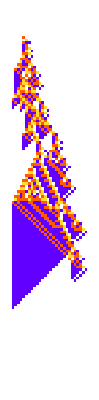
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},Row[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,200}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2],Spacer[1]]]
```

## Beyond Biology: The Fundamental Problem of Medicine

```mathematica
GraphicsRow[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1},{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,220}]&/@{<|{23,202}->3|>,<|{23,202}->3,{57,214}->3|>,<|{23,202}->3,{44,209}->2|>,<|{23,202}->3,{34,208}->3|>,<|{23,202}->3,{26,204}->1|>,<|{23,202}->3,{31,202}->3|>,<|{23,202}->3,{35,207}->3|>,<|{23,202}->3,{52,211}->3|>,<||>},Spacer[25],{{2},{-2}}]]
```

-Graphics-

## Comparing Engineered Systems to Adapted Systems

### Engineered

```mathematica
GraphicsRow[Values[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#MatrixData,0},3#Period,Mesh->None,ViewPoint->{-2.5858505040989677,-2.1357760886689436,0.4492634745014381},ImageSize->{Automatic,200}]&/@Select[Select[{{"[◼]", "Data"}}["$LifeData"],#Class==="Gun"&],#Year<1990&]]]
```

-Graphics-

## Comparing Engineered Systems to Adapted Systems

### Adapted

```mathematica
(*aares=ParallelTable[(SeedRandom[34578+i];With[{max=400},Nest[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=TestCALifeTime[CellularAutomaton["GameOfLife",{u,0},max]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]),{i,200}];*)
```

```mathematica
(*CloudExport[aares,"WXF",Permissions->"Public"];*)
```

```mathematica
aares = Import["https://www.wolframcloud.com/obj/2f6183db-0aea-47a2-8f81-f7d4df6449b2"];
```

```mathematica
GraphicsRow[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#[[1]],0},1+#[[2]],ImageSize->{Automatic,12Sqrt[#[[2]]+4]}]&/@aares[[{14,165,101, 194,112,87,65,47,30,33}]]]
```

-Graphics-

## A Minimal Model for Computer Security

## A Minimal Model for Computer Security

## There’s so much more to explore!